## Section 3: Separation of time scales: Slow-fast analysis (nb : X here means d in the manuscript)

Since we are interested in the dimorphism at the major locus, we assume that the allelic sizes of population are positive.

```mathematica
hypothesis={m1>0,g1>0,etaA>0,m2>0,g2>0,alpha>0,lambda>0,N1A>0,N1a>0,N2A>0,N2a>0};
```

System (17) of section 2.2

```mathematica
eN1a = N1a*(1-(N1a+N1A)-g1(z1a+etaa+1)^2-e^2g)+m2*alpha*N2a-m1*N1a;
eN1A = N1A*(1-(N1a+N1A)-g1(z1A+etaA+1)^2-e^2g)+m2*alpha*N2A-m1*N1A;
eN2a = N2a*(lambda-(N2a+N2A)-g2(z2a+etaa-1)^2-e^2g)+m1/alpha*N1a-m2*N2a;
eN2A = N2A*(lambda-(N2a+N2A)-g2(z2A+etaA-1)^2-e^2g)+m1/alpha*N1A-m2*N2A;
ez1a = e^2*2*g1(-1-etaa-z1a)+((z1A-z1a)/2)N1A/(N1a+N1A)+m2*alpha*N2a/N1a*(z2a-z1a);
ez1A = e^2*2*g1(-1-etaA-z1A)+((z1a-z1A)/2)N1a/(N1a+N1A)+m2*alpha*N2A/N1A*(z2A-z1A);
ez2a = e^2*2*g2(1-etaa-z2a)+((z2A-z2a)/2)N2A/(N2a+N2A)+m1/alpha*N1a/N2a(z1a-z2a);
ez2A = e^2*2*g2(1-etaA-z2A)+((z2a-z2A)/2)N2a/(N2a+N2A)+m1/alpha*N1A/N2A(z1A-z2A);
```

Change of variable (formula (18) of section 3) : da = (z2a - z1a)/(2 e^2) ; dA = (z2A - z1A)/(2 e^2) , za* = (z2a + z1a)/2 ; zA* = (z2A + z1A)/2 ; X = ( (zA* - za*)/2 )/ e^2, Z = (zA* + za*) / 2. At the end, we keep (da, dA, X, Z). Let us write the new equations (using z1a = Z - e^2 X - e^2 da  ; z2a = Z - e^2 X + e^2 da ; z1A = Z + e^2 X - e^2 dA ; z2A = Z+ e^2 X + e^2 dA):

```mathematica
MChangeOfVar = {{-1/(2e^2),1/(2e^2),0,0}, {0,0,-1/(2e^2),1/(2e^2)},{-1/(4e^2),-1/(4e^2),1/(4e^2),1/(4e^2)},{1/4,1/4,1/4,1/4}};
InverseChangeOfVar=Inverse[MChangeOfVar].{da,dA,X,Z};
ChangeOfVar = {z1a->InverseChangeOfVar[[1]], z2a->InverseChangeOfVar[[2]], z1A->InverseChangeOfVar[[3]], z2A->InverseChangeOfVar[[4]]};
eN1a  = ReplaceAll[eN1a,ChangeOfVar];
eN2a  = ReplaceAll[eN2a,ChangeOfVar];
eN1A  = ReplaceAll[eN1A,ChangeOfVar];
eN2A  = ReplaceAll[eN2A,ChangeOfVar];
eda =ReplaceAll[(ez2a-ez1a)/(2e^2),ChangeOfVar]//Simplify;
edA =ReplaceAll[(ez2A-ez1A)/(2e^2),ChangeOfVar]//Simplify;
eX = ReplaceAll[(ez1A+ez2A-ez1a-ez2a)/(4e^2),ChangeOfVar]//Simplify;
eZ = ReplaceAll[(ez1A+ez2A+ez1a+ez2a)/(4e^2),ChangeOfVar]//Simplify;
```

The system that we obtain is the system (19) of section 3.

## Section 3.1 Analysis of the fast equilibria

The following expressions are the two system S0(Z) and SL(Z) of section 3.

```mathematica
{eN1a0,eN2a0,eN1A0, eN2A0,eda0,edA0,eX0,eZ0} = Simplify[{eN1a,eN2a,eN1A, eN2A,eda,edA,eX,eZ}/.e->0];
```

### Subsystem (N1a, N2a, N1A, N2A) : S0(Z)

#### Stability (Proposition 3.3 of section 3.1.2)

```mathematica
manifoldN = {eN1a0==0,eN2a0==0,eN1A0==0,eN2A0==0};
```

The following matrix is JS0 (formula (24)) of section 3.1.2.

```mathematica
JacN = {{- N1a-m2*alpha*N2a/N1a,m2*alpha,-N1a,0},{m1/alpha,- N2a-m1/alpha*N1a/N2a,0,-N2a},{-N1A,0,- N1A-m2*alpha*N2A/N1A,m2*alpha},{0,-N2A,m1/alpha,- N2A-m1/alpha*N1A/N2A}};
```

Let us verify the Routh Hurwitz criterion for JacN.

```mathematica
ChiJacN =CharacteristicPolynomial[JacN,X];
{a0,a1,a2,a3,a4} =Simplify[CoefficientList[ChiJacN,X]];
```

```mathematica
RouthHurwitzChiJacN = 
{Simplify[a3>0,Assumptions->hypothesis],
Simplify[Expand[a3*a2-a4*a1]>0,Assumptions->hypothesis],
Simplify[Expand[(a3*a2-a4*a1)*a1-a3^2*a0]>0,Assumptions->hypothesis],
Simplify[a0>0,Assumptions->hypothesis]}
```

{True,True,True,(N1A N2a-N1a N2A)^2>0}

The last line shows that all entries are positive under the assumptions that m > 0 and N1a, N1A, N2a, N2A > 0 and YA > Ya (for a0, the determinant). Hence, the Routh-Hurwitz criterion is verified and the eigenvalues of the jacobian are located in the left open half plane.

### Subsystem on (da, dA, X) (in the manuscrit, X=d) : SL(Z)

#### Resolution (Proposition 3.2 of section 3.1.1)

The following matrix is B in the manuscript.

```mathematica
ClearAll[X,dA,da];
Jac3 = Simplify[D[{eX0,edA0,eda0},{{X, dA, da}}]];
```

We check that the subsystem on (X, dA, da) is in fact affine. The result is the r.h.s of SL(Z) in section 3.

```mathematica
vector=Simplify[Jac3.{X,dA,da}-{eX0,edA0,eda0}];
```

We check that the jacobian is invertible, as soon as N1A, N1a, N2A, N2a > 0. (Proposition 3.2 of section 3.1.1)

```mathematica
Simplify[Det[Jac3]<0,Assumptions->hypothesis]
```

True

The next expression is equivalent to the one in the proof of Proposition 3.2 of section 3.1.1.

```mathematica
Simplify[Det[Jac3],Assumptions->hypothesis]
```

-((2 m1^2 N1a^2 N1A^2 (N1a+N1A) (N2a+N2A)+alpha^3 m2 N2a N2A (N2a+N2A) (2 alpha m2 N1A N2a N2A+N1a (2 alpha m2 N2a N2A+N1A (N2a+N2A)))+alpha m1 (N1a N1A (N1a+N1A)^2 N2a N2A+2 alpha m2 (N1A^3 N2a^2 N2A+N1a^3 N2a N2A^2+N1a^2 N1A N2A^2 (2 N2a+N2A)+N1a N1A^2 N2a^2 (N2a+2 N2A))))/(4 alpha^2 N1a N1A (N1a+N1A) N2a N2A (N2a+N2A)))

Hence, the subsytem admits a unique solution expressed in terms of N1A, N1a, N2A, N2a.

#### Stability (Proposition 3.4 of section 3.1.2)

Stability relies on the specter of the jacobian of the subsystem Jac3. We also check that the Routh Hurwitz criterion applies.

```mathematica
ChiJac3 =CharacteristicPolynomial[Jac3,X];
{b0,b1,b2,b3} =CoefficientList[ChiJac3,X];
B0=b0/b3; B1=b1/b3; B2=b2/b3;
Simplify[b3<0,Assumptions->hypothesis]
```

True

As the leading coefficient is negative, the Routh Hurwitz criterion becomes : b0 < 0, b2 < 0, b1*b2 > b3*b0

```mathematica
RouthHurwitzChiJac3 = {Simplify[b0<0,Assumptions->hypothesis],Simplify[b2<0,Assumptions->hypothesis],Simplify[b1*b2-b0*b3>0,Assumptions->hypothesis]}
```

{True,True,True}

Therefore, all the eigenvalues of Jac3 lie in the open half plane. (result of Proposition 3.4 of section 3.1.2)

## Section 4: Analysis of the stability of dimorphism in the limit system

First, let us change variable according to the assumption of symmetrical environment:

```mathematica
symmetry= {m1->m,m2->m,g1->g,g2->g,lambda->1,alpha->1,etaa->-eta,etaA->eta};
{eN1asym,eN2asym,eN1Asym, eN2Asym,edasym,edAsym,eXsym,eZsym} = Simplify[{eN1a,eN2a,eN1A, eN2A,eda,edA,eX,eZ}/.symmetry];
{eN1a0sym,eN2a0sym,eN1A0sym, eN2A0sym,eda0sym,edA0sym,eX0sym,eZ0sym} = Simplify[{eN1asym,eN2asym,eN1Asym, eN2Asym,edasym,edAsym,eXsym,eZsym}/.e->0];
```

The last system is the l.h.s of the system (25).

#### Existence (Proposition 4.1)

The first four following equations are the system (20) of Proposition 3.1. The return of the call is the system (27) in the proof of Proposition 4.1 (at the exception that in the expression of N10sym and N20sym, YA has not been substituted to its expression). The last line verifies that YAsym = 1/Yasym and N10sym=N20sym.

```mathematica
ClearAll[Ya,YA,N1,N2]
YA0= g1/(alpha*m2)(etaA+etaa+2Z+2)(etaA-etaa)/2*(Sqrt[1+m1*m2/(4*g1*g2*(etaA/2-etaa/2)^2*(1-(etaA/2+etaa/2+Z)^2))]+1);
Ya0 = g1/(alpha*m2)(etaA+etaa+2Z+2)(etaA-etaa)/2*(Sqrt[1+m1*m2/(4*g1*g2*(etaA/2-etaa/2)^2*(1-(etaA/2+etaa/2+Z)^2))]-1);
N10= 1 - g1*(1+Z+etaA)^2-m1+m2*alpha*YA;
N20= lambda - g2*(-1+Z+etaA)^2-m2+m1/alpha/YA;
{YA0sym,Ya0sym,N10sym,N20sym}=Simplify[{YA0,Ya0,N10,N10}/.Z->0/.symmetry]
{Simplify[N10sym==N20sym],Simplify[(YA0sym==1/Ya0sym)]}
```

{(eta g (2+√(4+m^2/(eta^2 g^2))))/m,(eta g (-2+√(4+m^2/(eta^2 g^2))))/m,1-(1+eta)^2 g+m (-1+YA),1-(1+eta)^2 g+m (-1+YA)}

{True,True}

The following cell is meant to justify the expression of da0, dA0, and d0 (here X0sym) of the proof of Proposition 4.1 (first line). We first do a change of variable to replace (N2A, N2a, N2A, N2a) by their expression in terms of Ya, YA, N1 and N2. The last line verifies that the expression of the first line actually solves SL(Z).

```mathematica
{X0sym,dA0sym,da0sym} ={-(2 g (1+eta-YA^2+eta YA^2))/YA,(g (1+eta+YA-eta YA))/(m (1+YA)),(g (1+eta+YA-eta YA))/(m (1+YA))};
MChangeOfVarN1N2YAYa = {{1,0,1,0},{0,1,0,1},{-Ya,1,0,0},{0,0,-YA,1}};
{N1a0sym,N2a0sym,N1A0sym,N2A0sym} = Simplify[LinearSolve[MChangeOfVarN1N2YAYa,{N1sym,N2sym,0,0}]/.Z->0/.Ya->1/YA/.N1->N2];
Jac3sym =Simplify[Jac3/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Z->0/.symmetry];
vectorsym = Simplify[vector/.symmetry];
Simplify[-vectorsym+Jac3sym.{X0sym,dA0sym,da0sym} =={0,0,0}/.YA->YA0sym]
```

True

With the following computations, we verify the result of the proposition 4.1.

```mathematica
Simplify[eZ0==0/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Z->0/.YA->YA0sym/.symmetry]
```

True

The latter shows that (N1A0, N1a0, N2A0, N2a0, X0, dA0, da0, Z = 0) is an equilibrium.

#### Stability (paragraph below Proposition 4.1 in Section 4)

There exists a neighborhood U of the dimor. sym. equilibrium and a smooth function phi such that each (N1A, N2A, N1a, N2a, da, dA, X) of the manifold defined by (eN1A=0, eN1a=0, eN2A=0, eN2a=0, affinesystem=0) and in U can be parametrized by Z: (N1A, N1a, N2A, N2a, da, dA, X) = phi(Z). Next step is to formulate the limit problem as :  G(Z,phi(Z)) = 0 and dZ/dt = F(Z,phi(Z)), Z in P(U) (projection of U along the Z coordinate). We want to compute: dF/dZ(0) + dF/Dphi * phi’(0) with phi’(0) obtained with G(Z,phi(Z)) = 0, hence phi’(Z) = - (dG/dphi)^{-1} dG/dZ.

```mathematica
ClearAll[Ya,YA,N1,N2]
F=eZ0sym;
dFdZ0 = Simplify[D[F,Z]];
dFDphi0 = Simplify[D[F,{{N1a,N2a,N1A,N2A,X,dA,da}}]/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Ya->1/YA/.N1->N2/.Z->0];
DGDphi0 = Simplify[D[{eN1a0sym,eN2a0sym,eN1A0sym,eN2A0sym,eX0sym,edA0sym,eda0sym},{{N1a,N2a,N1A,N2A,X,dA,da}}]/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Ya->1/YA/.N1->N2/.Z->0];
dGdZ0 = Simplify[D[{eN1a0sym,eN2a0sym,eN1A0sym,eN2A0sym,eX0sym,edA0sym,eda0sym},Z]/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Ya->1/YA/.N1->N2/.Z->0];
Dphi0 = -Simplify[LinearSolve[DGDphi0,dGdZ0]/.N1a->N1a0sym/.N2a->N2a0sym/.N1A->N1A0sym/.N2A->N2A0sym/.X->X0sym/.dA->dA0sym/.da->da0sym/.Ya->1/YA/.N1->N2/.Z->0];
ClearAll[dF0,dF0explicit];
dF0 = Simplify[dFdZ0 + dFDphi0.Dphi0];
```

-2 g

{-(2 (-1+eta) g (-1+m+g (1+eta^2-eta √(4+m^2/(eta^2 g^2)))) YA)/(1+YA),-(2 (1+eta) g (-1+m+g (1+eta^2-eta √(4+m^2/(eta^2 g^2)))))/(1+YA),(2 (1+eta) g (-1+m+g (1+eta^2-eta √(4+m^2/(eta^2 g^2)))))/(1+YA),(2 (-1+eta) g (-1+m+g (1+eta^2-eta √(4+m^2/(eta^2 g^2)))) YA)/(1+YA),0,0,0}

Right now, everything is still expressed in terms of N2 and YA (computations are faster than with their explicit expressions N20 and YA0). Let’s take a look at the explicit expression by replacing N2 and YA:

```mathematica
dF0explicit = Simplify[Simplify[dF0/.YA->YA0sym/.N2->N20sym]];
```

#### Section 4: Numerical analysis of the stability region

The analytical criterion of stability is that dF0explicit is negative. Here, Eta is a fixed parameter storing the value of eta (major effect).

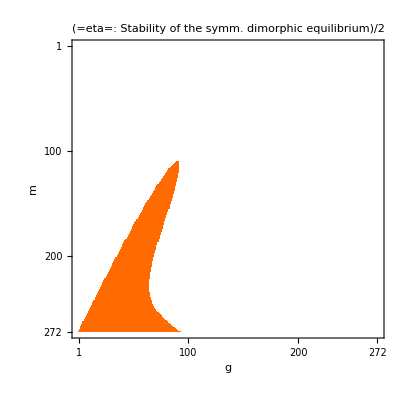

```mathematica
ClearAll[eta,Eta,Mstability,f];
Eta=1/2;
M=Range[0.01,3,0.011];
Nm=Length[M];
G=Range[0.01,3,0.011];
Ng=Length[G];
Mstability=Array[2&,{Nm,Ng}];
For[i=1,i<Nm+1,i++,
For[j=1,j<Ng+1,j++,
	Mstability[[Nm+1-i]][[j]]=Boole[(Simplify[dF0explicit/.m->M[[i]]/.g->G[[j]]/.eta->Eta]<0)]*Boole[(Simplify[N20sym/.YA->YA0sym/.m->M[[i]]/.g->G[[j]]/.eta->Eta]>0)];

];
];
MatrixPlot[Mstability,FrameLabel->{m,g},PlotLabel->"=eta=: Stability of the symm. dimorphic equilibrium"Eta]
```